# Support Vector Machines

## Demonstrace funkce a použití SVM klasifikátoru

## Příprava prostředí

Nejprve načteme všechny potřebné knihovny.

```mathematica
SetDirectory[NotebookDirectory[]];
Quiet[<<MathSVM`];
Needs["VectorAnalysis`"];
```

A inicializujeme funkce, které jsou dále používány.

```mathematica
SVMPlotMy[α_,X_?MatrixQ,y_,opts___]:=Module[{x1range,x2range,sv,df,x1,x2,K},K=KernelFunction/.{opts}/.Options[SVMPlot];
x1range={x1,Min[X[[All,1]]],Max[X[[All,1]]]};
x2range={x2,Min[X[[All,2]]],Max[X[[All,2]]]};
sv=SupportVectors[α,y];
df=Total[α*y*Map[K[{x1,x2},#]&,X]]+Bias[α,X,y,opts];
Show[ListPlot[X[[Flatten[sv]]],PlotStyle->{Hue[0.6],PointSize[0.020]}],ListPlot[Extract[X,Position[y,1]],PlotStyle->{Red}],ListPlot[Extract[X,Position[y,-1]],PlotStyle->{Green}],ImplicitPlot[df==0,x1range,x2range,PlotStyle->{Thick}],ImplicitPlot[df==1,x1range,x2range,PlotStyle->Dashing[{.01,.01}]],ImplicitPlot[df==-1,x1range,x2range,PlotStyle->Dashing[{.01,.01}]],PlotRange->All(*,RemainingOptions[{KernelFunction},opts]*)]];
KernelRBF[x_,z_, b_]:=Exp[-b (x-z) (x-z)];
KernelPolynomial[x_,z_,c_,d_Integer]:=(c+x z)^d;
```

## Použití SVM na jednoduchých datech

Vygenerujeme data, která budeme pomocí SVM klasifikovat.

```mathematica
points=20;
x=Join[RandomReal[NormalDistribution[-2,1],{points/2,2}],
RandomReal[NormalDistribution[2,1],{points/2,2}]];
y=Join[Table[1,{points/2}],Table[-1,{points/2}]];
```

Data si můžeme prohlédnout v grafu.

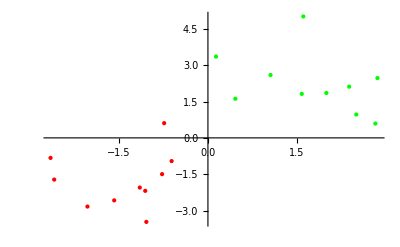

```mathematica
ListPlot[{Extract[x,Position[y,1]],Extract[x,Position[y,-1]]},PlotStyle->{Red,Green}, PlotRange->All]
```

Vidíme, že data jsou velmi jednooduchá, obsahují dvě třídy- červenou a zelenou. Na první pohled je jasné, že data jsou lineárně separabilní. Nyní na datech natrénujeme SVM klasifikátor a zobrazíme si jeho výstup.

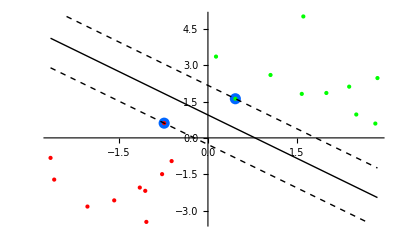

```mathematica
t=0.01;
a=SeparableSVM[x,y,t];
SVMPlotMy[a,x,y]
```

V grafu vidíme dvě opěrné roviny (přímky) zobrazené čárkovaně, Rovina, pomocí je prováděna klasifikace je zobrazena tlustou plnou čárou - vše nad rovinou patří do zelené třády, vše pod ní patří do červené třídy. Modrou barvou jsou zvýrazněny opěrné vektory.

Dále si vygenerujeme trochu složitější data.

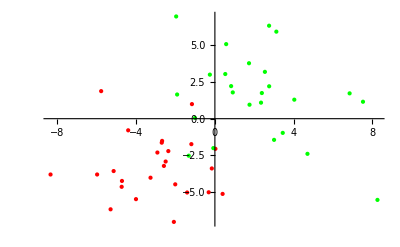

```mathematica
points2=50;
xx=Join[RandomReal[NormalDistribution[-3,2],{points2/2,2}],
RandomReal[NormalDistribution[2,3],{points2/2,2}]];
yy=Join[Table[1,{points2/2}],Table[-1,{points2/2}]];
ListPlot[{Extract[xx,Position[yy,1]],Extract[xx,Position[yy,-1]]},PlotStyle->{Red,Green}, PlotRange->All]
```

Jak je patrné z grafu, tyto data již není možné lineárně separovat. V tom případě můžeme pokračovat dvěmi způsoby. První a nejčastější způsob je přesunout se pomocí jádrové funkce do vyšší dimenze, ve které už budou data lineárně separabilní. Tomuto způsobu se budeme podrobně věnovat později. Druhá možnost je trvat na lineární separaci a připustit možnou chybu.

Zobrazíme si výstup lineární separace s povolenou chybou.

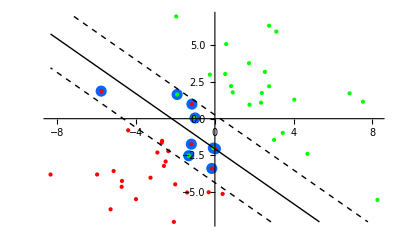

```mathematica
aa=NonseparableSVM[xx,yy,0.5,0.01];
SVMPlotMy[aa,xx,yy]
```

U SVM je možné nastavit si chybovou funkci, která určí jak moc je pro nás chyba významná. Klasifikátor se poté snaží tuto chybu minimalizovat. Na následujícím grafu je možné odzkoušet, jak se bude vyvýjet klasifikace s měnícím se významem chyby.

```mathematica
Manipulate[ab=NonseparableSVM[xx,yy,e,0.01];
SVMPlotMy[ab,xx,yy],{{e,0.5,"Význam chyby"},0.001,2},ContinuousAction->False]
```

Outer::normal: Nonatomic expression expected at position 2 in Outer[IdentityKernel, xx, xx, 1].

Outer::normal: Nonatomic expression expected at position 2 in Outer[Times, yy, yy].

Union::heads: Heads List and If at positions 2 and 1 are expected to be the same.

Part::partw: Part 5 of MathSVM`Private`GetIndexSets[If[yy . {} == 0, MathSVM`Private`α$613, Null], {}, {}, yy] does not exist.

Union::normal: Nonatomic expression expected at position 2 in If[yy . {} == 0, MathSVM`Private`α$613, Null] ∪ yy ∪ MathSVM`Private`GetIndexSets[If[yy . {} == 0, MathSVM`Private`α$613, Null], {}, {}, yy] ⟦ 5 ⟧.

Part::partw: Part 5 of MathSVM`Private`GetIndexSets[If[yy . {} == 0, MathSVM`Private`α$613, Null], {}, {}, yy] does not exist.

Union::normal: Nonatomic expression expected at position 2 in If[yy . {} == 0, MathSVM`Private`α$613, Null] ∪ yy ∪ MathSVM`Private`GetIndexSets[If[yy . {} == 0, MathSVM`Private`α$613, Null], {}, {}, yy] ⟦ 5 ⟧.

Union::heads: Heads List and If at positions 2 and 1 are expected to be the same.

Part::pspec: Part specification If[yy . {} == 0, MathSVM`Private`α$613, Null] ∪ yy ∪ MathSVM`Private`GetIndexSets[If[yy . {} == 0, MathSVM`Private`α$613, Null], {}, {}, yy] ⟦ 5 ⟧ is neither an integer nor a list of integers.

Part::pspec: Part specification Union[If[yy . {} == 0, MathSVM`Private`α$613, Null], {}, {}] is neither an integer nor a list of integers.

Part::pspec: Part specification If[yy . {} == 0, MathSVM`Private`α$613, Null] is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

## Jádrové funkce

Jádrové funkce jsou základmním triken, pomocí kterého se SVM přesouvá do vyšších dimenzí. (Opakovaným) Aplikováním těchto funkcí na data se provede jejich transformae do vyšší dimenze, kde je již možné je lineárně separovat nadrovinou.

Nejčastěji se jako jádrové funkce používají následující dvě.

## Polynomial kernel

Polynomiální kernel je jádrová funkce s následujícím předpisem k(x_1,x_2) = (x_1*x_2 +1)^d. Při jejím použití je třeba vhodně nastavit stupeň polynomu - parametr d.

Jak polynomiální kernel vypadá v závislosti na jeho stupni je možné si prohlédnout na následujícím grafu.

```mathematica
Manipulate[Plot3D[KernelPolynomial[x,z,1,d],{x,-4,4},{z,-4,4},ViewPoint->{-7.654,-1.091,4.608},PlotPoints->{30,30}],{{d,1,"Stupen polynomu"},1,20,1}]
```

Nyní necháme SVM, aby si transformovalo data do vyšší dimenze pomocí polynomiálního kernelu a následně provedlo klasifikaci. Ke klasifikaci použijeme stejná data jako v případě klasifikace s chybovou funkcí.  Graf umožnuje interaktivně nastavovat stupen polynomu.

```mathematica
Manipulate[pk=PolynomialKernel[#1,#2,t]&;
aab=NonseparableSVM[xx,yy,0.5,0.01, KernelFunction->pk];
SVMPlotMy[aab,xx,yy,KernelFunction->pk],{{t,1,"Stupen polynomu"},1,10,1},ContinuousAction->False]
```

Outer::normal: Nonatomic expression expected at position 2 in Outer[PolynomialKernel[#1, #2, FE`t$$4] &, xx, xx, 1].

Outer::normal: Nonatomic expression expected at position 2 in Outer[Times, yy, yy].

Union::heads: Heads List and If at positions 2 and 1 are expected to be the same.

Part::partw: Part 5 of MathSVM`Private`GetIndexSets[If[yy . {} == 0, MathSVM`Private`α$672, Null], {}, {}, yy] does not exist.

Union::normal: Nonatomic expression expected at position 2 in If[yy . {} == 0, MathSVM`Private`α$672, Null] ∪ yy ∪ MathSVM`Private`GetIndexSets[If[yy . {} == 0, MathSVM`Private`α$672, Null], {}, {}, yy] ⟦ 5 ⟧.

Part::pspec: Part specification If[yy . {} == 0, MathSVM`Private`α$672, Null] ∪ yy ∪ MathSVM`Private`GetIndexSets[If[yy . {} == 0, MathSVM`Private`α$672, Null], {}, {}, yy] ⟦ 5 ⟧ is neither an integer nor a list of integers.

Part::pspec: Part specification Union[If[yy . {} == 0, MathSVM`Private`α$672, Null], {}, {}] is neither an integer nor a list of integers.

Part::pspec: Part specification If[yy . {} == 0, MathSVM`Private`α$672, Null] is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Z grafů je patrné, že při použití nízkého stupně polynomu se SVM model nedoučuje, naopak při použití vysokého stupně je model přeučený. Vhodná hodnota stupně polynomu se hledá experimentálně, nejčastěji křížovou validací.

## RBF kernel

Je druhá často používaná jádrová funkce. Její předpis je následující k(x_1,x_2)e^(-(t(x_1-x_2))^2) Při použití je potřeba vhodně nastavit parametr t.

RBF kernel v závislosti na parametru t si můžete prohlédnout na následujícím grafu.

```mathematica
Manipulate[Plot3D[KernelRBF[x,z,t],{x,-10,10},{z,-10,10},ViewPoint->{3.849,6.909,4.295},PlotPoints->{30,30}],{{t,0.000001,"t"},0.000001,0.5}]
```

Nyní naučíme SVM za použití transformace dat pomocí RBF kernelu. Data použijeme stejná jako v případě polynomiálního kernelu.

Graf umožnuje interaktivně měnit patametr t.

```mathematica
Manipulate[RBFk=RBFKernel[#1,#2,t]&;
aaa=NonseparableSVM[xx,yy,0.5,0.01, KernelFunction->RBFk];
SVMPlotMy[aaa,xx,yy,KernelFunction->RBFk],{{t,0.02,"t"},0.0001,3,0.01},ContinuousAction->False]
```

Outer::normal: Nonatomic expression expected at position 2 in Outer[RBFKernel[#1, #2, FE`t$$2] &, xx, xx, 1].

Outer::normal: Nonatomic expression expected at position 2 in Outer[Times, yy, yy].

Union::heads: Heads List and If at positions 2 and 1 are expected to be the same.

Part::partw: Part 5 of MathSVM`Private`GetIndexSets[If[yy . {} == 0, MathSVM`Private`α$709, Null], {}, {}, yy] does not exist.

Union::normal: Nonatomic expression expected at position 2 in If[yy . {} == 0, MathSVM`Private`α$709, Null] ∪ yy ∪ MathSVM`Private`GetIndexSets[If[yy . {} == 0, MathSVM`Private`α$709, Null], {}, {}, yy] ⟦ 5 ⟧.

Part::pspec: Part specification If[yy . {} == 0, MathSVM`Private`α$709, Null] ∪ yy ∪ MathSVM`Private`GetIndexSets[If[yy . {} == 0, MathSVM`Private`α$709, Null], {}, {}, yy] ⟦ 5 ⟧ is neither an integer nor a list of integers.

Part::pspec: Part specification Union[If[yy . {} == 0, MathSVM`Private`α$709, Null], {}, {}] is neither an integer nor a list of integers.

Part::pspec: Part specification If[yy . {} == 0, MathSVM`Private`α$709, Null] is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Jak je z grafů výše vidět, pro nižší hodnoty parametru t se SVM ndoučuje, a pro vysoké hodnoty se silně přeučuje. Optimální hodnota parametru se určuje experimentálně, například křížovou validací.

## Ilustrace přechodu do vyšší dimenze

V této kapitole si podrobněji rozebereme transformaci dat do vyšší dimenze.

Nejprve si vygenerujeme data, na kterých budeme transformaci demonstrovat.

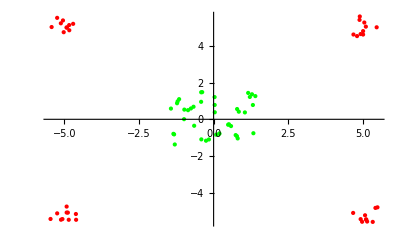

```mathematica
values = 40;
inRing=Join[ Join[RandomReal[{-5.5,-4.6},{values/4,1}],
RandomReal[{-5.6,-4.5},{values/4,1}],2],
Join[RandomReal[{5.5,4.6},{values/4,1}],
RandomReal[{5.6,4.5},{values/4,1}],2],
Join[RandomReal[{-5.5,-4.6},{values/4,1}],
RandomReal[{5.6,4.5},{values/4,1}],2],
Join[RandomReal[{5.5,4.6},{values/4,1}],
RandomReal[{-5.6,-4.5},{values/4,1}],2]];
inCentral =Join[RandomReal[{-1.5,1.5},{values,1}],
RandomReal[{-1.5,1.5},{values,1}],2];
inputData = Join[inRing,inCentral];
inputClasses=Join[Table[1,{values}],Table[-1,{values}]];
ListPlot[{Extract[inputData,Position[inputClasses,1]],Extract[inputData,Position[inputClasses,-1]]},PlotStyle->{Red,Green}, PlotRange->All]
```

Jak je patrné z grafu, data jsou lineárně neseparabilní. Proto použijeme polynomiální kernel k jejich trasformaci do tří rozměrů.

Nejprve si připravíme předpisy pro funkce používané později.

```mathematica
polynomDegree = 4;
RBFparam = 0.1;
KRBF= RBFKernel[#1,#2,RBFparam]&;
KPol=PolynomialKernel[#1,#2,polynomDegree]&;
KernelPolynomialSpec[x_]:={x[[1]],x[[2]],(1+x[[1]] x[[2]])^polynomDegree};
KernelRBFSpec[x_]:={x[[1]],x[[2]], Exp[-RBFparam (x[[1]]-x[[2]]) (x[[1]]-x[[2]])]};
```

Nyní můžeme provést samotnou transformaci dat.

```mathematica
higherDim = KernelPolynomialSpec/@inputData;
Show[ListPointPlot3D[{Extract[higherDim,Position[inputClasses,1]],Extract[higherDim,Position[inputClasses,-1]]},PlotStyle->{{Red,PointSize[Medium]},{Green,PointSize[Medium]}},PlotRange->All],
Plot3D[KernelPolynomial[x,z,1,polynomDegree],{x,-5.5,5.5},{z,-5.5,5.5},PlotPoints->{30,30},PlotRange->All,PlotStyle->Opacity[0.3],Mesh->None]]
```

-Graphics3D-

V grafu jsou vidět transformovaná data, a také funkce, pomocí které byla transformace provedena. Za povšimnutí stojí hodnoty osy z. Vidíme tedy, že data jsou po transformaci již lineárně separabilní pomocí roviny.

Najeme tedy opěrné roviny, které separují data.

```mathematica
vectors=Take[Sort[Join[Take[Sort[Extract[higherDim,Position[inputClasses,1]][[;;values/4]],#1[[3]]<#2[[3]]&],1],Take[Sort[Extract[higherDim,Position[inputClasses,1]][[values/4;;values/2]],#1[[3]]<#2[[3]]&],1],Take[Sort[Extract[higherDim,Position[inputClasses,1]][[values/2;;3*values/4]],#1[[3]]<#2[[3]]&],1],Take[Sort[Extract[higherDim,Position[inputClasses,1]][[3*values/4;;values]],#1[[3]]<#2[[3]]&],1]],#1[[3]]<#2[[3]]&],3];
vectors2=Sort[Join[Take[Sort[Extract[higherDim,Position[inputClasses,-1]],#1[[3]]<#2[[3]]&],1]]];
v1=vectors[[1]]-vectors[[2]];
v2=vectors[[3]]-vectors[[2]];
normal=CrossProduct[v1,v2];
aa=normal[[3]];
d=Dot[normal,vectors[[1]]];
formula=normal*{x,y,1};
formula = Plus@@formula;
formula=(formula-d)/-aa;
dd=Dot[normal,vectors2[[1]]];
formula2=normal*{x,y,1};
formula2 = Plus@@formula2;
formula2=(formula2-dd)/-aa;
F[x_,y_]:=(Total[normal*{x,y,1}]-d)/-aa;
F2[x_,y_]:=(Total[normal*{x,y,1}]-dd)/-aa;
```

Roviny si zobrazíme do předchozího obrázku.

```mathematica
formula3=normal*{x,y,1};
formula3 = Plus@@formula3;
ddd=Dot[normal,{0,0,Abs[F[0,0]-F2[0,0]]/2}];
formula3=((formula3-ddd)/-aa);
F3[x_,y_]:=(Total[normal*{x,y,1}]-ddd)/-aa;
Show[ListPointPlot3D[{Extract[higherDim,Position[inputClasses,1]],Extract[higherDim,Position[inputClasses,-1]]},PlotStyle->{{Red,PointSize[Medium]},{Green,PointSize[Medium]}},PlotRange->All],
 Plot3D[formula,{x,-5.5,5.5},{y,-5.5,5.5},Mesh->None,PlotStyle->Opacity[0.2],BoundaryStyle->{Red}],
Plot3D[formula2,{x,-5.5,5.5},{y,-5.5,5.5},Mesh->None,PlotStyle->Opacity[0.2],BoundaryStyle->{Green}],
Plot3D[formula3,{x,-5.5,5.5},{y,-5.5,5.5},Mesh->None,PlotStyle->Opacity[0.4],BoundaryStyle->{Thick}],ListPointPlot3D[vectors[[;;3]], PlotStyle->{PointSize[0.020],Hue[0.6]}],ListPointPlot3D[vectors2[[;;1]], PlotStyle->{PointSize[0.020],Hue[0.6]}],ViewPoint->{15,6,4}]
```

-Graphics3D-

Světlejší, barevně orámované roviny jsou opěrné roviny jednotlivých tříd, Černě orámovaná, nejvýraznější rovina je rovina, pomocí které se provádí klasifikace. V grafu jsou také zvýrazněny opěrné vektory modrou barvou.

Výslednou klasifikaci si můžeme přiblížit následujícím grafem.

```mathematica
range=10;
Show[Plot3D[KernelPolynomial[x,z,1,polynomDegree],{x,-range,range},{z,-range,range},PlotRange->All,PlotStyle->Opacity[0],Mesh->None,RegionFunction->Function[{x,y,z},z>F[x,y]],BoundaryStyle->{Dashing[{.001,.001}]}],Plot3D[KernelPolynomial[x,z,1,polynomDegree],{x,-range,range},{z,-range,range},PlotRange->All,PlotStyle->Opacity[0],Mesh->None,RegionFunction->Function[{x,y,z},z>F2[x,y]],BoundaryStyle->{Dashing[{.001,.001}]}],Plot3D[KernelPolynomial[x,z,1,polynomDegree],{x,-range,range},{z,-range,range},PlotRange->All,PlotStyle->Opacity[0],Mesh->None,RegionFunction->Function[{x,y,z},z>F3[x,y]],BoundaryStyle->{Thick}],ListPointPlot3D[{Extract[higherDim,Position[inputClasses,1]],Extract[higherDim,Position[inputClasses,-1]]},PlotStyle->{{Red,PointSize[Medium]},{Green,PointSize[Medium]}},PlotRange->All],ListPointPlot3D[vectors[[;;3]],PlotStyle->Directive[PointSize[Large],Opacity[0.5]]],ListPointPlot3D[vectors2[[;;1]],PlotStyle->Directive[PointSize[Large],Opacity[0.5]]],ViewPoint->{0,0,10}]
```

-Graphics3D-

Tlustá černá čára představuje výslednou klasifikaci a slabší čáry zobrazují opěrné roviny. Světle modře jsou zvýrazněny opěrné vektory.

## Použití SVM na reálných datech

V této poslední kapitole si ukážeme použítí SVM na reálných datech z databáze UCI. K tomuto účelu použijeme známá Iris data.

Nejprve si data načteme. Pozor, je potřeba připojení k internetu.

```mathematica
data=Import["http://ftp.ics.uci.edu/pub/machine-learning-databases/iris/iris.data"];
```

Dále provedeme jednoduché předzpracování dat. Nejprve rozdělíme data na vstupní a výstupní množinu. Výstupní množina obsahuje textové atributy, ty převedeme na číselné.

```mathematica
data2=Drop[data,-1];
inData=data2[[All,1;;4]];(*vstupní parametry*)
outDataTmp=data2[[All,5]];(*výstupní parametr*)outVal=Tally[outDataTmp][[All,1]];
encode=MapIndexed[#1->Normal[#2]&,outVal];
outData=Flatten[Flatten[outDataTmp]/.encode];
Func[x_,y_]:= If[y==x,1,-1];
outDataC1=Map[Func[#,1]&,outData];
outDataC2=Map[Func[#,2]&,outData];
outDataC3=Map[Func[#,3]&,outData];
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Níže jsou parametry použité pro klasifikaci. Jejich změnou a následným znovuvyhodnocením buňky, ve které se provádí klasifikace je možné provádět jednoduché experimenty.

```mathematica
PolDegree=10; (*stupen polynomu pro polynomiální kernel*)
RBFParam = 0.001;(*t parametr RBF kernelu*)
error=0.8;(*ohodnoceni chyby*)
precision=0.01; (*presnost*)
PolKer = PolynomialKernel[#1,#2,PolDegree]&;
RBFKer=RBFKernel[#1,#2,RBFParam]&;
```

SVM v základní podobě umí klasifikovat pouze do dvou tříd. Protože naše data obsahují tři třídy, musíme použít menší okliku.
Nejsnažši je zobecnění dat na dvě třídy následujícím způsobem. Vybereme jednu třídu, tu necháme beze změny a zbylé dvě třídy sloučíme do jedné (1 vs. others). Takto budedme postupovat pro všechny třídy. V našem případě takto získáme 3 datasety. Na každém datasetu natrénujeme jeden SVM model.

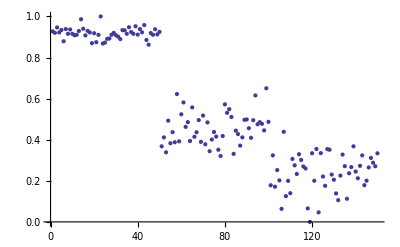

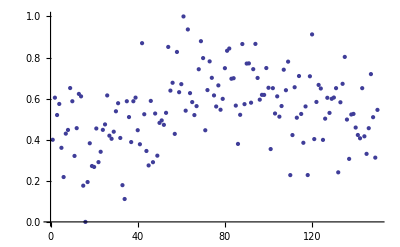

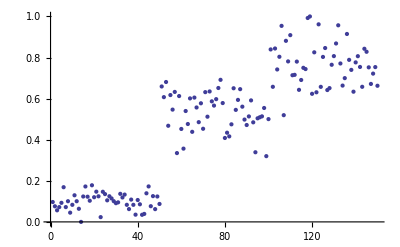

```mathematica
l=NonseparableSVM[inData,outDataC1,error,precision,KernelFunction->RBFKer];
out1=Rescale[inData.WeightVector[l,inData,outDataC1]];
ListPlot[out1]
ll=NonseparableSVM[inData,outDataC2,error,precision,KernelFunction->RBFKer];
out2=Rescale[inData.WeightVector[ll,inData,outDataC2]];
ListPlot[out2]
lll=NonseparableSVM[inData,outDataC3,error,precision, KernelFunction->RBFKer];
out3=Rescale[inData.WeightVector[lll,inData,outDataC3]];
ListPlot[out3]
```

Výstupem jsou tři grafy. První graf udává klasifikaci do první třídy, druhý graf do druhé třídy a třetí graf do třetí třídy. Výslednou klasifikaci určíme tak, že jako výstupní třídu bereme tu třídu, jejíž model dosahuje nejvyššího výstupu.

Zavedene fuknce, pomocí kterých porovnáme výstupy jednotlivých modelů.

```mathematica
MyCompare[a_,b_,c_]:=If[a>=b&&a≥c,1,If[b≥a&&b≥c,2,3]];
MyCorrect[a_,b_]:=If[a==b,1,0];
```

A zobrazíme si výslednou klasifikaci.

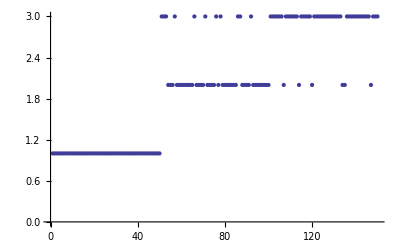

```mathematica
out={};
For[i=1,i≤Dimensions[out3][[1]],i++,
AppendTo[out,MyCompare[out1[[i]],out2[[i]],out3[[i]]]]
];
ListPlot[out]
```

Pro porovnámí si zobrazíme ještě správný výstup.

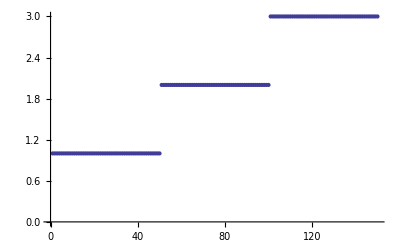

```mathematica
ListPlot[outData]
```

Úspěšnost klasifikace si vyjádříme ještě v procentech.

```mathematica
correct=0;
 For[i=1,i≤Dimensions[out3][[1]],i++,
correct+=MyCorrect[out[[i]],outData[[i]]];
];
N[correct/Dimensions[outData][[1]]*100,5]
```

88.667